# Računanje z Mathematico

Matematične izraze pišemo podobno, kot smo to počeli v LATEX-u; videli pa boste, da obstaja tudi nekaj razlik.
Primer izraza z eksponentom in množenjem: x^20+5 x/(2+x). Kot vidite, lahko namesto znaka za množenje napišete presledek (lahko pa tudi *).
Opozorilo: če boste samo kopirali izraz v nalogi v vnosno celico, to ne bo vedno delovalo.
Programerji lahko ta zvezek preletite na hitro in začnete brati Fast introduction for programmers.

### Subsection. naloga:

Mathematica je jezik, pa tudi uporabniški vmesnik. Preletite bližnjice na tipkovnici, da boste vedeli, kako si lahko olajšate delo.

### Subsection. naloga:

Pišemo lahko tudi grške črke in nekatere druge posebne znake. To naredimo tako, da stisnemo tipko Esc (napiše se znak “⋮”), nato ime posebnega znaka, npr. “alpha”, nato pa še enkrat .
V spodnjo celico napišite β in znak za stopinje °.

## Mathematica je lahko kalkulator

### Subsection. naloga:

Izračunajte vrednost izraza  ((20+316)^7-55)/(33·12)^3.
Izraz zapišite v celico pod tem navodilom in jo poženite tako, da stisnete Shift+Enter.

```mathematica
(*prostor za vaše rešitve*)
```

```mathematica
20+12321421414
```

12321421434

```mathematica
((20+316)^7-55)/(33*12)^3
```

483476023799709641/62099136

```mathematica
N[483476023799709641/62099136]
```

7.78555×10^9

```mathematica
((20+316)^7-55)/(33*12)^3
```

483476023799709641/62099136

```mathematica
2^3
```

8

### Subsection. naloga:

Izračunajte vrednost izraza  30! -20! +110

```mathematica
(*prostor za vaše rešitve*)
```

```mathematica
30!-20!+110
```

265252859812188625734300303360110

### Subsection. naloga:

Mathematica ima bogato knjižnico funkcij, ki jih lahko uporabite. Zapomnili si boste najbolj pogosto uporabne, za ostale pa je pomembno, da se jih naučite najti.
Za primer si poglejmo funkcijo N, ki vrne numerično vrednost izraza. Sprejme dva parametra, izraz in število decimalk. Funkcijo pokličete tako, da napišete ime funkcije, nato pa v oglatih oklepajih naštejete parametre: N[22/7,3]. Imena vseh funkcij in konstant se začnejo z veliko začetnico.

```mathematica
N[22/7,3] (* Poženite celico, da dobite rezultat *)
```

3.14

V eni celici lahko izračunate tudi več izrazov tako, da vsakega zapišete v svojo vrstico. Naslednje naloge rešujte v eni celici.
1. Izračunajte numerično vrednost izraza iz prejšnje naloge na 20 mest natančno.
2. S funkcijo Simplify poenostavite izraz  2^x+5a 2^x+2^(x+2). Poglejte si še kak primer uporabe te funkcije v dokumentaciji: spremenite ga in poženite celico.
3. V dokumentaciji poiščite funkcijo za računanje logaritmov in izračunajte log_10 10x.
4. Poiščite funkcijo, ki izračuna največji skupni delitelj števil, ter ga izračunajte za števila 536, 1248, 2320.

```mathematica
(*prostor za vaše rešitve*)
```

```mathematica
Simplify[2^x+5a 2^x+2^(x+2)]
```

5 2^x (1+a)

```mathematica
Log[10,10x]
```

Log[10 x]/Log[10]

```mathematica
FullSimplify[Log[10 x]/Log[10]]
```

1+Log[x]/Log[10]

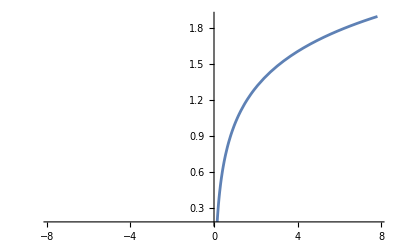

```mathematica
Plot[1+Log[x]/Log[10],{x,-7.817300674258531,7.817300674258531}]
```

```mathematica
GCD[538,1248,2320]
```

2

### Subsection. naloga:

V dokumentaciji poiščite funkcijo Derivative in njeni okrajšavi D in ‘.
Uporabite jo, da izračunate:
1. prvi in drugi odvod funkcije  arctan ,
2. prvi odvod funkcije (3x-2)^(1/3)/(√(2x+1)),
Če ste v eni od prejšnjih nalog določili vrednost x na 2, boste dobili čuden rezultat. Vrednost spremenljivke lahko počistimo s funkcijo Clear.

```mathematica
x=2
```

2

```mathematica
y x
```

2 x

```mathematica
Clear[x] 
(*prostor za vaše rešitve*)
```

```mathematica
D[ArcTan[x],{x,3}]
```

(8 x^2)/((1+x^2)^3)-2/((1+x^2)^2)

```mathematica
ArcTan'[x]
```

1/(1+x^2)

```mathematica
D[(3x-2)^(1/3)/(√(2x+1)),x]
```

1/(√(1+2 x) (-2+3 x)^(2/3))-(-2+3 x)^(1/3)/(1+2 x)^(3/2)

### Subsection. naloga:

1. Seštejte vsa soda števila na intervalu [1,100].
2. Izračunajte  ∑_(k=1)^∞ (k^2+1)/k^4

```mathematica
(*prostor za vaše rešitve*)
```

```mathematica
Sum[2k,{k,50}]
```

2550

```mathematica
Sum[k,{k,2,100,2}]
```

2550

```mathematica
Total[Select[Range[1,100],EvenQ]]
```

2550

```mathematica
Map[#*2&,Range[1,10]]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Sum[(k^2+1)/k^4,{k,1,Infinity}]
```

1/90 π^2 (15+π^2)

### Subsection. naloga:

Na kocko s stranico a postavimo drugo kocko s telesno diagonalo, enako stranici prve kocke, na drugo kocko spet tretjo s telesno diagonalo, enako stranici druge kocke, in to ponavljamo brez konca. Izračunajte višino tako dobljenega telesa: .

```mathematica
Sum[a/(√3)^i,{i,0,∞}]
```

-(3 a)/(-3+√3)

```mathematica
(*prostor za vaše rešitve*)
```

Izračunajte še prostornino tako dobljenega telesa.

```mathematica
(*prostor za vaše rešitve*)
```

```mathematica
Sum[(a/(√3)^i)^3,{i,0,∞}]
```

-(9 a^3)/(-9+√3)

### Subsection. naloga:

1. Izračunajte  lim_(x→0) (arctg (7x))/(arcsin (8x))
2. Izračunajte  lim_(x→π) (1+cos x)/(2 √(π x)-π-x)
3. Izračunajte levo limito:  lim_(x→0^-) |x|ctg x

```mathematica
(*prostor za vaše rešitve*)
```

```mathematica
Limit[ArcTan[7x]/ArcSin[8x],x->0]
```

7/8

```mathematica
Limit[(1+Cos[x])/(2 √(π x)-π-x),x->π]
```

-2 π

```mathematica
Limit[Abs[x]Cot[x],x->0,Direction->"FromBelow"]
```

-1

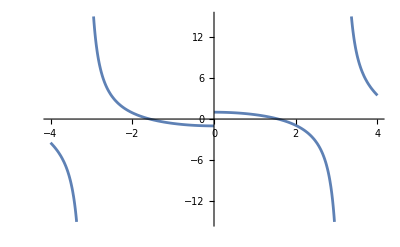

```mathematica
Plot[Abs[x]Cot[x],{x,-4,4}]
```

## Spremenljivke in funkcije

### Subsection. naloga:

Vrednosti izrazov lahko spravimo v spremenljivko, takole:

```mathematica
g=6.674 10^(−11)
```

6.674×10^-11

```mathematica
ClearAll[x,y]
```

```mathematica
f[x_,y_]:=x^2+y^2
```

```mathematica
f[3,4]
```

25

```mathematica
x1=1/0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

1. V dokumentaciji poiščite definicijo konstante Degree, ki jo uporabite, da napišete 1830° in 270°.
2. Ti dve vrednosti spravite v spremenljivki α in β.
3. Izračunajte vrednost izraza (sin α + sin β)/(cos^2(α - β) - sin^2(β-α)) za kota α=1830°  in  β=270°. Pri tem uporabite spremenljivki, ki se ju ravno definirali.
Če ne želite, da se izpiše vrednost nekega izraza, lahko tisto vrstico končate s podpičjem ;.

```mathematica
(*prostor za vaše rešitve*)
```

```mathematica
α=1830°
```

1830 °

```mathematica
β=270°
```

270 °

```mathematica
(Sin [α]+Sin[ β])/(Cos[α-β]^2-Sin[β-α]^2)
```

1

### Subsection. naloga:

1. Priredite polinom  x^7+2 x^6-80 x^5+232 x^4+175 x^3-826 x^2+256x-1056  spremenljivki p.
2. Razcepite ta polinom na linearne in kvadratne faktorje s pomočjo funkcije Factor.
3. Polinom razcepite še na same linearne faktorje. Funkciji boste morali povedati, da želite upoštevati tudi kompleksne ničle oz. da naj išče rešitve v obsegu realnih števil razširjenim s številom i.
V dokumentaciji poglejte, kako funkciji Factor določite razširitev (ko boste našli ime nastavitve, vam bo pri pisanju pomagal vmesnik).

```mathematica
(*prostor za vaše rešitve*)
p=x^7+2x^6-80x^5+232x^4+175x^3-826x^2+256x-1056
```

-1056+256 x-826 x^2+175 x^3+232 x^4-80 x^5+2 x^6+x^7

```mathematica
Factor[p]
```

(-4+x)^2 (-3+x) (2+x) (11+x) (1+x^2)

```mathematica
Factor[p,Extension->I]
```

(-4+x)^2 (-3+x) (-ⅈ+x) (ⅈ+x) (2+x) (11+x)

### Subsection. naloga:

1. Priredite polinom  (x^2 (y-1)-x^3 y^5+(x-1)^7 x y (x^2+2x y+y^3))^2  spremenljivki q.
2. Razširite ga tako, da dobite vsoto monomov. Poiščite ustrezno funkcijo v dokumentaciji.
3. Razvijte polinom po potencah x  (koeficienti bodo polinomi v y). Pomagajte si s funkcijo Collect.
4. S funkcijo Exponent poiščite najvišji potenci spremenljivk, ki se pojavita v polinomu.

```mathematica
(*prostor za vaše rešitve*)
```

```mathematica
q[x_,y_]:=(x^2(y-1)-x^3 y^5+(x-1)^7 x y(x^2+2x y+y^3))^2
```

```mathematica
Expand[q[x,y]]
```

x^4-2 x^4 y+2 x^5 y-14 x^6 y+42 x^7 y-70 x^8 y+70 x^9 y-42 x^10 y+14 x^11 y-2 x^12 y+5 x^4 y^2-30 x^5 y^2+99 x^6 y^2-196 x^7 y^2+301 x^8 y^2-518 x^9 y^2+1071 x^10 y^2-2020 x^11 y^2+3005 x^12 y^2-3432 x^13 y^2+3003 x^14 y^2-2002 x^15 y^2+1001 x^16 y^2-364 x^17 y^2+91 x^18 y^2-14 x^19 y^2+x^20 y^2-4 x^4 y^3+32 x^5 y^3-140 x^6 y^3+504 x^7 y^3-1596 x^8 y^3+4088 x^9 y^3-8036 x^10 y^3+12016 x^11 y^3-13728 x^12 y^3+12012 x^13 y^3-8008 x^14 y^3+4004 x^15 y^3-1456 x^16 y^3+364 x^17 y^3-56 x^18 y^3+4 x^19 y^3+2 x^3 y^4-10 x^4 y^4-14 x^5 y^4+294 x^6 y^4-1386 x^7 y^4+3962 x^8 y^4-7994 x^9 y^4+12010 x^10 y^4-13728 x^11 y^4+12012 x^12 y^4-8008 x^13 y^4+4004 x^14 y^4-1456 x^15 y^4+364 x^16 y^4-56 x^17 y^4+4 x^18 y^4-2 x^3 y^5+16 x^4 y^5-68 x^5 y^5+252 x^6 y^5-798 x^7 y^5+2044 x^8 y^5-4018 x^9 y^5+6008 x^10 y^5-6864 x^11 y^5+6006 x^12 y^5-4004 x^13 y^5+2002 x^14 y^5-728 x^15 y^5+182 x^16 y^5-28 x^17 y^5+2 x^18 y^5+4 x^3 y^6-56 x^4 y^6+362 x^5 y^6-1454 x^6 y^6+3990 x^7 y^6-7966 x^8 y^6+11942 x^9 y^6-13658 x^10 y^6+11970 x^11 y^6-7994 x^12 y^6+4002 x^13 y^6-1456 x^14 y^6+364 x^15 y^6-56 x^16 y^6+4 x^17 y^6+4 x^5 y^7-28 x^6 y^7+84 x^7 y^7-140 x^8 y^7+140 x^9 y^7-84 x^10 y^7+28 x^11 y^7-4 x^12 y^7+x^2 y^8-14 x^3 y^8+91 x^4 y^8-364 x^5 y^8+1001 x^6 y^8-2002 x^7 y^8+3003 x^8 y^8-3432 x^9 y^8+3003 x^10 y^8-2002 x^11 y^8+1001 x^12 y^8-364 x^13 y^8+91 x^14 y^8-14 x^15 y^8+x^16 y^8+2 x^4 y^9-14 x^5 y^9+42 x^6 y^9-70 x^7 y^9+70 x^8 y^9-42 x^9 y^9+14 x^10 y^9-2 x^11 y^9+x^6 y^10

```mathematica
Collect[Expand[q[x,y]],x]
```

x^20 y^2+x^2 y^8+x^19 (-14 y^2+4 y^3)+x^18 (91 y^2-56 y^3+4 y^4+2 y^5)+x^17 (-364 y^2+364 y^3-56 y^4-28 y^5+4 y^6)+x^13 (-3432 y^2+12012 y^3-8008 y^4-4004 y^5+4002 y^6-364 y^8)+x^3 (2 y^4-2 y^5+4 y^6-14 y^8)+x^15 (-2002 y^2+4004 y^3-1456 y^4-728 y^5+364 y^6-14 y^8)+x^16 (1001 y^2-1456 y^3+364 y^4+182 y^5-56 y^6+y^8)+x^14 (3003 y^2-8008 y^3+4004 y^4+2002 y^5-1456 y^6+91 y^8)+x^12 (-2 y+3005 y^2-13728 y^3+12012 y^4+6006 y^5-7994 y^6-4 y^7+1001 y^8)+x^7 (42 y-196 y^2+504 y^3-1386 y^4-798 y^5+3990 y^6+84 y^7-2002 y^8-70 y^9)+x^9 (70 y-518 y^2+4088 y^3-7994 y^4-4018 y^5+11942 y^6+140 y^7-3432 y^8-42 y^9)+x^5 (2 y-30 y^2+32 y^3-14 y^4-68 y^5+362 y^6+4 y^7-364 y^8-14 y^9)+x^11 (14 y-2020 y^2+12016 y^3-13728 y^4-6864 y^5+11970 y^6+28 y^7-2002 y^8-2 y^9)+x^4 (1-2 y+5 y^2-4 y^3-10 y^4+16 y^5-56 y^6+91 y^8+2 y^9)+x^10 (-42 y+1071 y^2-8036 y^3+12010 y^4+6008 y^5-13658 y^6-84 y^7+3003 y^8+14 y^9)+x^8 (-70 y+301 y^2-1596 y^3+3962 y^4+2044 y^5-7966 y^6-140 y^7+3003 y^8+70 y^9)+x^6 (-14 y+99 y^2-140 y^3+294 y^4+252 y^5-1454 y^6-28 y^7+1001 y^8+42 y^9+y^10)

```mathematica
Exponent[x,y]
```

0

```mathematica
Exponent[q[x,y],y]
```

10